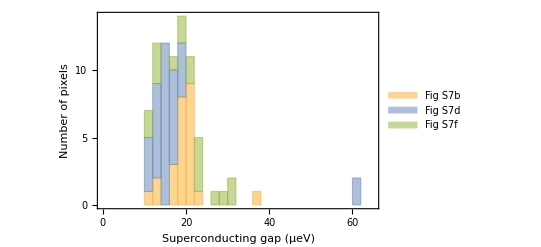

```mathematica
(* the data to be histogrammed are digitizations made using ImageJ of the figure panels S7b, S7d, and S7f of the supporting material of "Interferometric Single-Shot Parity Measurement in InAs-Al Hybrid Devices" by Microsoft Azure Quantum, Nature 638,651-655 (2025) *)

(* The values in these tables are digitised values of the magnitudes of the measured topological gaps, in μeV.  The histograms plot the number of observations in bins of size 0.2 μeV versus the magnitude of the gap. *)

datafigS7b={10.86,13.14,13.14,16.,16.29,16.29,18.57,18.57,18.57,18.57,18.57,18.57,18.86,18.86,21.25,21.25,21.25,21.25,21.25,21.25,21.5,21.5,21.5,23.75,36.83};
datafigS7d={10.6,10.6,10.6,10.6,12.1,12.4,12.4,12.4,12.4,12.4,12.4,14.1,14.1,14.1,14.4,14.4,14.4,14.4,14.4,14.4,14.4,14.4,14.4,16.8,16.8,16.8,16.8,16.8,17.1,17.1,18.8,18.8,18.8,18.8,60.0,60.0};
datafigS7f={10.6,10.6,13.1,13.1,13.1,16.6,19.1,19.1,21.7,21.7,23.8,23.8,23.8,23.8,26.9,29.0,31.5,31.5};
Histogram[Flatten[{datafigS7b}],{2},PlotRange->{{0,65},Automatic},Axes->False,Frame->True,FrameStyle->Black,BaseStyle->{FontSize->14,FontFamily->"Helvetica"},FrameLabel->{"Superconducting gap (μeV)","Number of pixels",None,None},
FrameTicks->{{{0,5,10},None},{{0,10,20,30,40,50,60},None}},PlotLabel->"Fig S7b"];
Histogram[Flatten[{datafigS7d}],{2},PlotRange->{{0,65},Automatic},Axes->False,Frame->True,FrameStyle->Black,BaseStyle->{FontSize->14,FontFamily->"Helvetica"},FrameLabel->{"Superconducting gap (μeV)","Number of pixels",None,None},
FrameTicks->{{{0,5,10},None},{{0,10,20,30,40,50,60},None}},PlotLabel->"Fig S7d"];
Histogram[Flatten[{datafigS7f}],{2},PlotRange->{{0,65},Automatic},Axes->False,Frame->True,FrameStyle->Black,BaseStyle->{FontSize->14,FontFamily->"Helvetica"},FrameLabel->{"Superconducting gap (μeV)","Number of pixels",None,None},
FrameTicks->{{{0,5,10},None},{{0,10,20,30,40,50,60},None}},PlotLabel->"Fig S7f"];

Histogram[{datafigS7b,datafigS7d,datafigS7f},{2},PlotRange->{{0,65},Automatic},
Axes->False,Frame->True,FrameStyle->Black,
BaseStyle->{FontSize->14,FontFamily->"Helvetica"},
FrameLabel->{"Superconducting gap (μeV)","Number of pixels",None,None},
FrameTicks->{{{0,5,10},None},{{0,10,20,30,40,50,60},None}},ChartLayout->"Stacked",ChartLegends->Placed[{"Fig S7b", "Fig S7d", "Fig S7f"},{.76,.75}]]
```

```mathematica
Quantile[Flatten[Join[{datafigS7b,datafigS7d,datafigS7f}]],0.5]
```

16.8

```mathematica
Quantile[Flatten[Join[{datafigS7b,datafigS7d,datafigS7f}]],0.9]
```

23.8